```mathematica
ClearGlobal[];
```

```mathematica
$Assumptions={ {Lx, Ly, Lz}∈Reals, Lx>0, Ly>0, Lz>0, L>0, Ixx>0};
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["Calc3DMatProp`"]
```

### Geometry and topology definition

```mathematica
nodes={{0,0,0},{Lx,0,0},{0,Ly,0},{0,0,Lz},{Lx,0,Lz},{0,Ly,Lz},{Lx,Ly,0},{Lx,Ly,Lz},{Lx/2,Ly/2,0},{Lx/2,Ly/2,Lz},{0,Ly/2,Lz/2},{Lx,Ly/2,Lz/2},{Lx/2,0,Lz/2},{Lx/2,Ly,Lz/2}}/.{Lx->L,Ly->L, Lz->L};
beams={{3,1},{1,2},{2,7},{7,3},{4,5},{5,8},{8,6},{6,4},{1,4},{2,5},{7,8},{3,6},
{13,1},{13,2},{13,5},{13,4},{12,2},{12,7},{12,8},{12,5},{14,7},{14,3},{14,6},{14,8},{11,3},{11,1},{11,4},{11,6},{10,4},{10,5},{10,8},{10,6},{9,1},{9,2},{9,7},{9,3}};
shells={{09,01,02},{09,02,07},{09,07,03},{09,03,01},{10,04,05},{10,05,08},{10,08,06},{10,06,04},{11,01,04},{11,04,06},{11,06,03},{11,03,01},{13,01,02},{13,02,05},{13,05,04},{13,04,01},{12,02,05},{12,05,08},{12,08,07},{12,07,02},{14,07,03},{14,03,06},{14,06,08},{14,08,07}};
nnodes=Dimensions[nodes]⟦1⟧;
nbeams=Dimensions[beams]⟦1⟧;
nshells=Dimensions[shells]⟦1⟧;
a1=nodes⟦2⟧-nodes⟦1⟧;a2=nodes⟦3⟧-nodes⟦1⟧;a3=nodes⟦4⟧-nodes⟦1⟧;
V=a1.a2×a3;
```

```mathematica
{αs,βs,γs}={(Es (ν-1))/(2 ν^2+ν-1),-(Es ν)/(2 ν^2+ν-1),Es/(2 ν+2)};
```

```mathematica
Eqs={{1,1,1,1,1,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,1}};
(* Eqs={{1,1,1,1,1,1,1,1,0}}; *)
{B0,Bϵ}=MakeB0andBe[Eqs,nodes]//Simplify;
```

```mathematica
rbeams={{3},{4},{5},{6},{7},{8},{10},{11},{12},{21},{22},{23},{24},{25},{26},{27},{28},{33},{34},{35},{36}};
rshells={{5},{6},{7},{8},{17},{18},{19},{20},{21},{22},{23},{24}};
```

```mathematica
ρ=CalcModelVolume[nodes, Delete[beams,rbeams],Delete[shells,rshells],  {A, 2 Iyy, Iyy, Iyy},{Es,ν,t}]/V//Simplify;
```

```mathematica
Graph1=DrawUnitCell[nodes/.{ L->1}, beams,shells]
Graph2=DrawUnitCell[nodes/.{ L->1},  Delete[beams,rbeams],Delete[shells,rshells]]
```

-Graphics3D-

-Graphics3D-

```mathematica
(* Export["cubicCellFCC.gif",Rasterize[Graph1, ImageResolution->600,Background->None]]
Export["cubicCellPrimFCC.gif",Rasterize[Graph2, ImageResolution->600,Background->None]] *)
```

## Find material stiffness matrix

### Only beams

```mathematica
Kuc=Make3DStiffMatrix[nodes, Delete[beams,rbeams], Delete[shells,rshells],{Es,Es/(2(1+ν))},{A, 2 Iyy, Iyy, Iyy},{Es,ν,t},{1,0,0}];
```

```mathematica
D0=Simplify[LinearSolve[Simplify[B0ᵀ.Kuc.B0], -Simplify[B0ᵀ.Kuc.Bϵ]]];
dϵ=B0.D0+Bϵ//Simplify;
Kmat=1/V dϵᵀ.Kuc.dϵ//Simplify;
```

```mathematica
L^2/(A Es)Kmat/.{Iyy->0}//Simplify//MatrixForm
```

(1+√2 | 1/(√2) | 1/(√2) | 0 | 0 | 0
1/(√2) | 1+√2 | 1/(√2) | 0 | 0 | 0
1/(√2) | 1/(√2) | 1+√2 | 0 | 0 | 0
0 | 0 | 0 | 1/(√2) | 0 | 0
0 | 0 | 0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 1/(√2))

```mathematica
L^4/(Es Iyy)Kmat/.{ A->0}//Simplify//MatrixForm
```

(24 √2 | -12 √2 | -12 √2 | 0 | 0 | 0
-12 √2 | 24 √2 | -12 √2 | 0 | 0 | 0
-12 √2 | -12 √2 | 24 √2 | 0 | 0 | 0
0 | 0 | 0 | (6 (5+4 √2+2 (2+√2) ν))/(5+4 ν) | 0 | 0
0 | 0 | 0 | 0 | (6 (5+4 √2+2 (2+√2) ν))/(5+4 ν) | 0
0 | 0 | 0 | 0 | 0 | (6 (5+4 √2+2 (2+√2) ν))/(5+4 ν))

### Only shells

```mathematica
Kuc=Make3DStiffMatrix[nodes, Delete[beams,rbeams], Delete[shells,rshells],{Es,Es/(2(1+ν))},{A, 2Iyy, Iyy, Iyy},{Es,ν,t},{0,1,0}];
```

```mathematica
D0=Simplify[LinearSolve[Simplify[B0ᵀ.Kuc.B0], -Simplify[B0ᵀ.Kuc.Bϵ]]];
dϵ=B0.D0+Bϵ//Simplify;
Kmat=1/V dϵᵀ.Kuc.dϵ//Simplify;
```

```mathematica
L/(Es t) Kmat//Simplify
```

{{-2/(-1+ν^2),ν/(1-ν^2),ν/(1-ν^2),0,0,0},{ν/(1-ν^2),-2/(-1+ν^2),ν/(1-ν^2),0,0,0},{ν/(1-ν^2),ν/(1-ν^2),-2/(-1+ν^2),0,0,0},{0,0,0,1/(2+2 ν),0,0},{0,0,0,0,1/(2+2 ν),0},{0,0,0,0,0,1/(2+2 ν)}}

### Only plates

```mathematica
Kuc=Make3DStiffMatrix[nodes, Delete[beams,rbeams], Delete[shells,rshells],{Es,Es/(2(1+ν))},{A, 2Iyy, Iyy, Iyy},{Es,ν,t},{0,0,1}];
```

```mathematica
D0=Simplify[LinearSolve[Simplify[B0ᵀ.Kuc.B0], -Simplify[B0ᵀ.Kuc.Bϵ]]];
dϵ=B0.D0+Bϵ//Simplify;
Kmat=1/V dϵᵀ.Kuc.dϵ//Simplify;
```

```mathematica
L^3/(Es t^3)Kmat//Simplify
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,-(8 (-153+48 ν+4 ν^2))/(27 (-7+2 ν) (-1+ν^2)),0,0},{0,0,0,0,-(8 (-153+48 ν+4 ν^2))/(27 (-7+2 ν) (-1+ν^2)),0},{0,0,0,0,0,-(8 (-153+48 ν+4 ν^2))/(27 (-7+2 ν) (-1+ν^2))}}

### Everything

```mathematica
Kuc=Make3DStiffMatrix[nodes, Delete[beams,rbeams], Delete[shells,rshells],{Es,Es/(2(1+ν))},{A, 2Iyy, Iyy, Iyy},{Es,ν,t},{1,1,1}];
```

```mathematica
D0=Simplify[LinearSolve[Simplify[B0ᵀ.Kuc.B0], -Simplify[B0ᵀ.Kuc.Bϵ]]];
```

```mathematica
dϵ=B0.D0+Bϵ//Simplify;
Kmat=1/V dϵᵀ.Kuc.dϵ//Simplify;
{α, β, γ}={Kmat[[1,1]], Kmat[[1,2]], Kmat[[6,6]]};
```

### Some plots

```mathematica
{α, β, γ}={Kmat[[1,1]], Kmat[[1,2]], Kmat[[6,6]]};
```

```mathematica
parplots=Simplify[Evaluate[{{ρ,(α+2β)/((αs+2βs) ρ)},{ρ,(α-β)/((αs-βs) ρ)},{ρ,γ/(γs ρ)}}/.{A->d^2, Iyy->d^4/12, Gm->Es/(2(1+ν))}/.{L->λ1 d, t->λ2 d, ν->3/10}]];
```

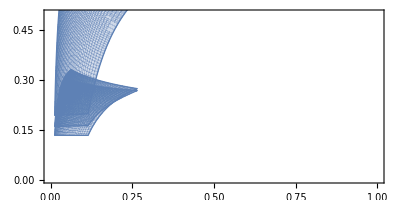

```mathematica
ParametricPlot[parplots, {λ1,10,30},{λ2,0,0.5},PlotRange->{{0, 1},{0,.5}}]
```

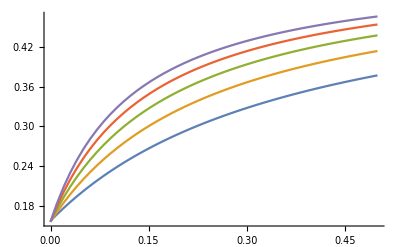

```mathematica
Plot[Evaluate[Table[Simplify[α/(αs ρ)/.{A->d^2, Iyy->d^4/12, Gm->Es/(2(1+ν))}/.{L->λ1 d, t->λ2 d, ν->3/10}],{λ1,10,30,5}]],{λ2,0,0.5}]
```

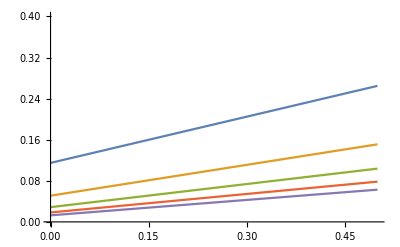

```mathematica
Plot[Evaluate[Table[Simplify[ρ/.{A->d^2, Iyy->d^4/12, Gm->Es/(2(1+ν))}/.{L->λ1 d, t->λ2 d, ν->3/10}],{λ1,10,30,5}]],{λ2,0,.5}, PlotRange->{0, 0.4}]
```

### Element stresses

```mathematica
Cmat=Inverse[Kmat]//Simplify;
```

```mathematica
BeamForces=Simplify[Table[GetBeamForces[kk,dϵ.{1,0,-1,0,0,0},nodes,beams,{Es,Es/(2 (1+ν))},{A,2 Iyy,Iyy,Iyy}],{kk,1,nbeams}]/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}];
```

```mathematica
N1=Simplify[GetBeamForces[1,dϵ.Cmat.{1,1,1,0,0,0},nodes,beams,{Es,Es/(2 (1+ν))},{A,2 Iyy,Iyy,Iyy}]/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}][[1,1]];
M1=0;
```

```mathematica
N2=Simplify[GetBeamForces[2,dϵ.Cmat.{1,0,-1,0,0,0},nodes,beams,{Es,Es/(2 (1+ν))},{A,2 Iyy,Iyy,Iyy}]/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}][[1,1]];
M2=Simplify[GetBeamForces[15,dϵ.Cmat.{1,0,-1,0,0,0},nodes,beams,{Es,Es/(2 (1+ν))},{A,2 Iyy,Iyy,Iyy}]/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}][[2,2]];
```

Part::partd: Part specification {0,0,(364 d^2 λ1^2)/(546 √2+91 (2+Power[«2»]) λ1^2+340 λ1^3 λ2),0,(91 √2 d^3 λ1^3)/(546 √2+91 (2+Power[«2»]) λ1^2+340 λ1^3 λ2),0}⟦1,1⟧ is longer than depth of object.

```mathematica
N3=0;
M3=Simplify[GetBeamForces[1,dϵ.Cmat.{0,0,0,1,0,0},nodes,beams,{Es,Es/(2 (1+ν))},{A,2 Iyy,Iyy,Iyy}]/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}][[2,2]];
```

Part::partd: Part specification {0,0,(91 d^2 λ1^2 (217 √2+2560 λ1 λ2^3))/(637 (46+Times[«2»])+«3»+λ1^2 (39494+Times[«2»])),0,(91 d^3 λ1^3 (217 √2+2560 λ1 λ2^3))/(1274 (46+Times[«2»])+8960 (52+Times[«2»]) λ1 λ2^3+358400 λ1^4 λ2^4+140 √2 λ1^3 λ2 (217+Times[«2»])+λ1^2 (78988+Times[«2»])),0}⟦2,2⟧ is longer than depth of object.

```mathematica
ParametricPlot[Simplify[Evaluate[{{ρ,N1/A},{ρ,N2/A},{ρ,N3/A}}/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}]],{λ1,10,30},{λ2,0,0.5},AspectRatio->Full]
```

-Graphics-

```mathematica
ParametricPlot[Simplify[Evaluate[{{ρ,M1/(d A)},{ρ,M2/(d A)},{ρ,M3/(d A)}}/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}]],{λ1,10,30},{λ2,0,0.5},AspectRatio->Full]
```

Part::partd: Part specification {0,0,1.14273 d^2,0,4.04075 d^3,0}⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification {0,0,0.696876 d^2,0,3.48488 d^3,0}⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification {0.,0.,1.14273 d^2,0.,4.04075 d^3,0.}⟦2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[Evaluate[Table[Simplify[M2/(d A)/.{A->d^2, Iyy->d^4/12, Gm->Es/(2(1+ν))}/.{L->λ1 d, t->λ2 d, ν->3/10}],{λ1,10,30,5}]],{λ2,0,.5}]
```

Part::partd: Part specification {0,0,(36400 d^2)/(546 √2+9100 (2+Power[«2»])+340000 λ2),0,(91000 √2 d^3)/(546 √2+9100 (2+Power[«2»])+340000 λ2),0}⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification {0,0,(81900 d^2)/(546 √2+20475 (2+Power[«2»])+1147500 λ2),0,(307125 √2 d^3)/(546 √2+20475 (2+Power[«2»])+1147500 λ2),0}⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification {0,0,(145600 d^2)/(546 √2+36400 (2+Power[«2»])+2720000 λ2),0,(728000 √2 d^3)/(546 √2+36400 (2+Power[«2»])+2720000 λ2),0}⟦2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
ParametricPlot[Simplify[Evaluate[{{ρ,N3/A},{ρ,M3/(d A)}}/.{A->d^2,Iyy->d^4/12,Gm->Es/(2 (1+ν))}/.{L->λ1 d,t->λ2 d,ν->3/10}]],{λ1,10,30},{λ2,0,0.5},AspectRatio->Full]
```

Part::partd: Part specification {0,0,0.696876 d^2,0,3.48488 d^3,0}⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification {0.,0.,0.696876 d^2,0.,3.48488 d^3,0.}⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification {0,0,0.699196 d^2,0,3.99591 d^3,0}⟦2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-